## Define the analytical solution and its derivatives

```mathematica
DSolve[y'[x]+x y[x] == x,y[x],x]
```

{{y[x]→1+ⅇ^(-x^2/2) C[1]}}

```mathematica
D[1+ⅇ^(-x^2/2),x]
```

-ⅇ^(-x^2/2) x

```mathematica
D[1+ⅇ^(-x^2/2),{x,2}]
```

-ⅇ^(-x^2/2)+ⅇ^(-x^2/2) x^2

```mathematica
ya[x_]:=1+ⅇ^(-x^2/2)
```

```mathematica
dyadx[x_]:=-ⅇ^(-x^2/2) x
```

```mathematica
d2yadx2[x_]:=-ⅇ^(-x^2/2)+ⅇ^(-x^2/2) x^2
```

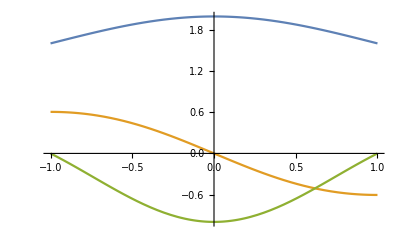

```mathematica
Plot[{ya[x],dyadx[x],d2yadx2[x]},{x,-1,1}]
```